```mathematica
Clear[pp,pu,ss,sv,svu,sa];
SetDirectory[NotebookDirectory[]]
```

/home/pi/ext/repos/HASTE/testing/SphereSources

```mathematica
pp=ReadList["Source-pp.txt",Number,RecordLists->True];
pu=ReadList["Source-pu.txt",Number,RecordLists->True];
ss=ReadList["Source-ss.txt",Number,RecordLists->True];
sv=ReadList["Source-sv.txt",Number,RecordLists->True];
svu=ReadList["Source-svu.txt",Number,RecordLists->True];
sa=ReadList["Source-sa.txt",Number,RecordLists->True];
```

```mathematica
ListPointPlot3D[{sv[[;;,6;;8]],sa[[;;,6;;8]]},BoxRatios->1]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{sv[[;;,2;;4]],sa[[;;,2;;4]]},BoxRatios->1]
```

-Graphics3D-

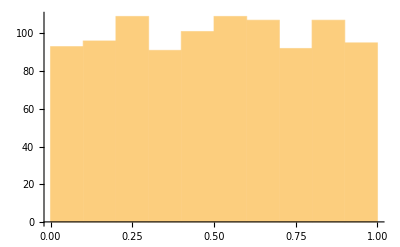

```mathematica
Histogram[pu[[;;,1]]]
```

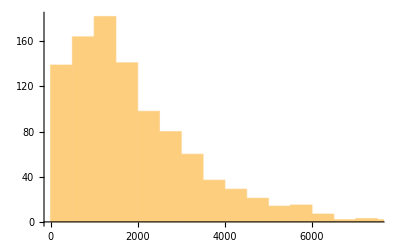

```mathematica
Histogram[pp[[;;,5]]]
```